# Computational Science

## Machine Learning for Physicists Project: Unsupervised and supervised analysis of protein sequences

This notebook is 100% human-made and has been created without any LLM.

Paul Cousin

Université Paris Cité • 2025/2026

## Note to the reader

Cells colored in blue will be code cells.

Cells colored in pink will be text comments.

## Import and format data

```mathematica
formatData[s_String]:=Module[{string=s},
string//=StringSplit[#,">"]&;
string//=StringDelete[#,"\n"]&;
string//=StringReplace[#,"sequence_"~~x:NumberString~~" functional_"~~y:("true"|"false")~~z__~~WordBoundary:>x~~","~~y~~","~~z]&;string//=StringSplit[#,","]&;
string/.{x_,y_,z_}:>{x,y=="true",z}
];
```

formatData is a function that formats the content of the .faa files which is encapsulated in  and  in the following cell.

```mathematica
natSeq=formatData@;
artSeq=formatData@;
```

Here is an example of how a sequence is now formatted.

```mathematica
natSeq[[1]]
```

{1,True,-TSENPLLALREKISALDEKLLALLAERRELAVEVGKAKLLSHRPVRDIDRERDLLERLITLGK-AHHLDAHYITRLFQLIIEDSVLTQQALLQQH}

## Task 1: One-hot encoding of protein sequence data

```mathematica
characterMap={"A"->1,"C"->2,"D"->3,"E"->4,"F"->5,"G"->6,"H"->7,"I"->8,"K"->9,"L"->10,"M"->11,"N"->12,"P"->13,"Q"->14,"R"->15,"S"->16,"T"->17,"V"->18,"W"->19,"Y"->20};
```

```mathematica
vectorize[seq_]:=SparseArray[If[#!="-",#->1,{}],20]&/@Replace[characterMap]/@StringPartition[seq,1];
```

```mathematica
natSeqHot=SparseArray[vectorize/@natSeq[[;;,3]]];
artSeqHot=SparseArray[vectorize/@artSeq[[;;,3]]];
```

All the sequences have been one-hot encoded in the SparseArray format.

```mathematica
natSeqHot[[1]]
```

SparseArray[…]

```mathematica
ArrayPlot@Transpose@natSeqHot[[1]]
```

-Graphics-

## Task 2: Dimensional reduction and visualization of sequence space

The data is stored in a 3-dimensional tensor. Its dimensions are:

```mathematica
Dimensions@natSeqHot
```

{1130,96,20}

We need to create a 1130×1130 covariance matrix from this data. To do this we need to combine two 96×20 matrices together and obtain a sort of distance. To do that, we can just count the number of elements they have in common by multiplying the two term by term and computing the total. For example:

```mathematica
Total[natSeqHot[[1]]*natSeqHot[[2]],2]
```

23

```mathematica
dim=Dimensions[natSeqHot][[1]];
cov=Table[Total[natSeqHot[[i]]*natSeqHot[[j]],2],{i,dim},{j,dim}];
```

```mathematica
ArrayPlot@cov
```

-Graphics-

```mathematica
eigen=Eigensystem[N@cov,3];
```

```mathematica
m=eigen[[1,1]]*({eigen[[2,1]]}ᵀ.{eigen[[2,1]]})+eigen[[1,2]]*({eigen[[2,2]]}ᵀ.{eigen[[2,2]]});
```

```mathematica
ArrayPlot@m
```

-Graphics-

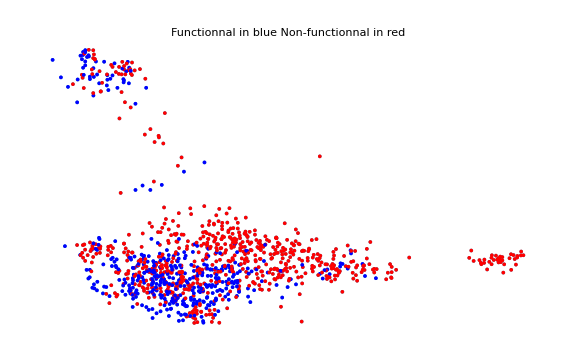

```mathematica
ListPlot[
Transpose[{
eigen[[1,1]]*Total[eigen[[2,1]]*natSeqHot,{2,3}],
eigen[[1,2]]*Total[eigen[[2,2]]*natSeqHot,{2,3}],
If[#,Blue,Red]&/@natSeq[[;;,2]]
}]/.{x_,y_,z_}:>Style[{x,y},z],
Axes->False,PlotRange->Full,ImageSize->Large,PlotLabel->"Functionnal in blue\nNon-functionnal in red"
]
```

```mathematica
ListPointPlot3D[
Transpose[{
eigen[[1,1]]*Total[eigen[[2,1]]*natSeqHot,{2,3}],
eigen[[1,2]]*Total[eigen[[2,2]]*natSeqHot,{2,3}],
eigen[[1,3]]*Total[eigen[[2,3]]*natSeqHot,{2,3}],
If[#,Blue,Red]&/@natSeq[[;;,2]]
}]/.{x_,y_,z_,c_}:>Style[{x,y,z},c],
Axes->False,PlotRange->Full,ImageSize->Large,PlotLabel->"Functionnal in blue\nNon-functionnal in red"
]
```

-Graphics3D-